```mathematica
pts={A->{0,1.9},B->{0.5,3},C->{3,3.1}};
Apt=A/. pts;Bpt=B/. pts;Cpt=C/. pts;

midAB=(Apt+Bpt)/2;
v=Bpt-Apt;
n={-v[[2]],v[[1]]};

t = ((Cpt-midAB).n)/(n.n);
Cproj = midAB+t n ;

a=Norm[Apt-midAB];
c=Norm[Cpt-Cproj];
l=Norm[midAB-Cproj];

Grid[{{"a",a},{"c",c},{"l",l}},Frame->All]

(*riesenie ako koren derivacie L =0*)
eq=2 x/Sqrt[a^2+x^2]-(l-x)/Sqrt[c^2+(l-x)^2]==0;
Solve[eq,x]
xsol=NSolve[eq,x]
FindRoot[eq,{x,0}]

(*Riesenie ako minimum L*)
Lfun[x_]:=2 Sqrt[a^2+x^2]+Sqrt[c^2+(l-x)^2];
xsol=NArgMin[{Lfun[x],0<=x},x]
Lmin=Lfun[xsol]

xmax=Norm[Cproj-midAB];

Manipulate[
dir=Normalize[Cproj-midAB]; (*smerovy vektor osi*)
SptOpt=midAB+xsol*dir;
Module[{Spt,L},
Spt=midAB+x*dir;
L=Norm[Apt-Spt]+Norm[Bpt-Spt]+Norm[Cpt-Spt];
top =Graphics[{
Orange,PointSize[0.02],Point[SptOpt],
Orange,Text["S optimalne",SptOpt,{-1.5,-1.5}],

Red,PointSize[0.015],Point[{Apt,Bpt,Cpt}],
Black,Text["A",Apt,{-1.5,-1.5}],Text["B",Bpt,{-1.5,-1.5}],Text["C",Cpt,{-1.5,-1.5}],
Black,Line[{Apt,Bpt}],
Dashed,Blue,Line[{midAB,Cproj}],
Dashed,Green,Line[{Cproj,Cpt}],
Purple,PointSize[0.015],Point[midAB],
Darker@Green,PointSize[0.02],Point[Spt],
Darker@Green,Text["S",Spt,{-1.5,-1.5}],
Black,Line[{Apt,Spt}],
Text["AS",(Apt+Spt)/2,{0,-1}],
Black,Line[{Bpt,Spt}],
Text["BS",(Bpt+Spt)/2,{0,-1}],
Black,Line[{Cpt,Spt}],
Text["CS",(Cpt+Spt)/2,{0,-1}]
},
PlotRange->All,Axes->True,PlotLabel->Row[{"L(T) = ",NumberForm[L,{Infinity,6}]}]
]
],
{x,0,xmax,Appearance->"Labeled"}
]
```

a | 0.604152
c | 1.7297
l | 2.23454

{{x→0.246096}}

{{x→0.246096}}

{x→0.246096}

0.246097

3.94018

Axis | x* | S* | Lmin
AB | 0.246097 | {0.474038,2.348165} | 3.940182
AC | 0.412596 | {1.346766,2.883085} | 4.189606
BC | 0.264312 | {1.760564,2.785899} | 4.528122

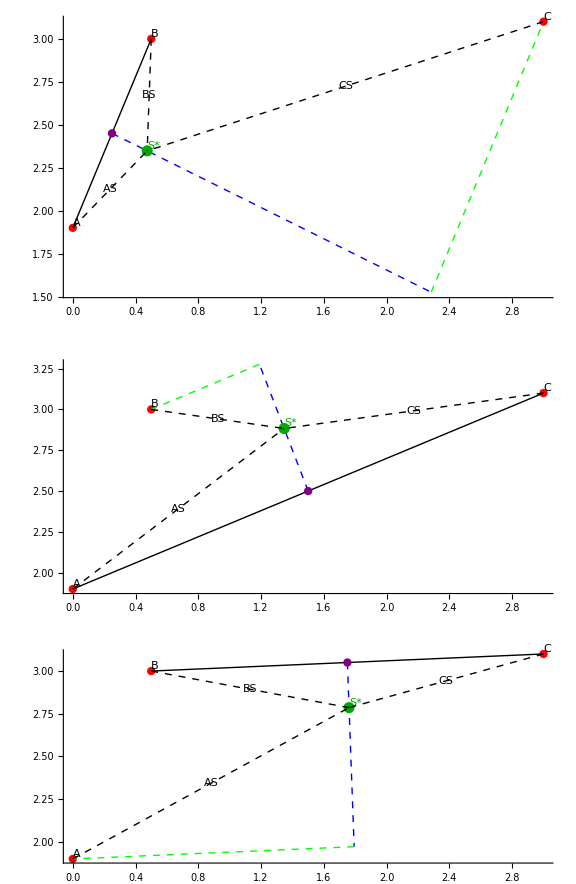

```mathematica
AxisMin[P_,Q_,R_]:=Module[{mid,v,n,t,Rproj,a,c,l,Lfun,xsol,dir,Sopt,Lmin},
mid=(P+Q)/2;
v=Q-P;
n={-v[[2]],v[[1]]};
t=((R-mid).n)/(n.n);
Rproj=mid+t*n;

a=Norm[P-mid];c=Norm[R-Rproj];
l=Norm[Rproj-mid];
Lfun[x_]:=2 Sqrt[a^2+x^2]+Sqrt[c^2+(l-x)^2];
xsol=NArgMin[{Lfun[x],0<=x<=l},x];
dir=Normalize[Rproj-mid];
Sopt=mid+xsol*dir;
Lmin=Lfun[xsol];

plot=Graphics[{Red,PointSize[0.015],Point[{Apt,Bpt,Cpt}],Black,Text["A",Apt,{-1.5,-1.5}],Text["B",Bpt,{-1.5,-1.5}],Text["C",Cpt,{-1.5,-1.5}],Black,Line[{P,Q}],Dashed,Blue,Line[{mid,Rproj}],Dashed,Green,Line[{Rproj,R}],Purple,PointSize[0.015],Point[mid],Darker@Green,PointSize[0.02],Point[Sopt],Darker@Green,Text["S*",Sopt,{-1.5,-1.5}],Black,Line[{Apt,Sopt}],Text["AS",(Apt+Sopt)/2,{0,-1}],Black,Line[{Bpt,Sopt}],Text["BS",(Bpt+Sopt)/2,{0,-1}],Black,Line[{Cpt,Sopt}],Text["CS",(Cpt+Sopt)/2,{0,-1}]},PlotRange->All,Axes->True
];

<|"mid"->mid,"proj"->Rproj,"x*"->xsol,"S*"->Sopt,"Lmin"->Lmin,"a"->a,"c"->c,"l"->l, "plot"->plot|>];

resAB=AxisMin[Apt,Bpt,Cpt];
resAC=AxisMin[Apt,Cpt,Bpt];
resBC=AxisMin[Bpt,Cpt,Apt];

Grid[Prepend[{{"AB",resAB["x*"],resAB["S*"],resAB["Lmin"]},{"AC",resAC["x*"],resAC["S*"],resAC["Lmin"]},{"BC",resBC["x*"],resBC["S*"],resBC["Lmin"]}}/. r_Real:>NumberForm[r,{Infinity,6}],{"Axis","x*","S*","Lmin"}],Frame->All]


GraphicsColumn[{resAB["plot"],resAC["plot"],resBC["plot"]},ImageSize->Large]
```